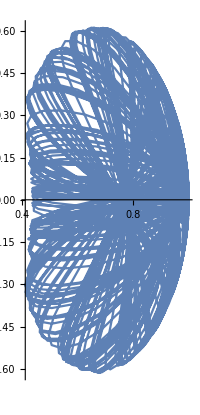

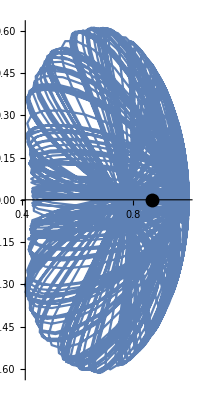

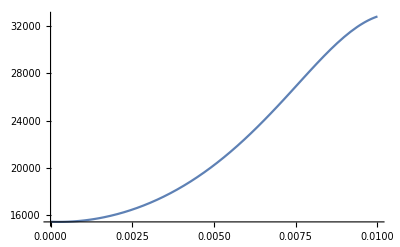

```mathematica
ClearAll[sol,s];
g=9.81;
l=1;
a=Pi;
s=2*Pi/3;
f=1/Cos[2*Pi/3];
q1=500;
q2=-500;
ϵ=1E-2;
m=1;

system={θ''[t]==(ϕ'[t]^2 Cos[θ[t]]*Sin[θ[t]]-(g/l)*Sin[θ[t]]-((q1*q2)/(m*l*l*ϵ*8*Pi*(l^2+f^2-2*l*f*(Sin[θ[t]]*Sin[s]*Cos[ϕ[t]-a]+Cos[θ[t]]*Cos[s]))^(3/2)))*(2*l*f*(Cos[θ[t]]*Sin[s]*Cos[ϕ[t]-a]-Sin[θ[t]]*Cos[s])))-0*θ'[t],ϕ''[t]==((((q1*q2)/(m*l*l*ϵ*8*Pi*(l^2+f^2-2*l*f*(Sin[θ[t]]*Sin[s]*Cos[ϕ[t]-a]+Cos[θ[t]]*Cos[s]))^(3/2)))*(2*f*l*Sin[θ[t]]*Sin[s]*Sin[ϕ[t]-a])-(2 ϕ'[t] θ'[t] Cos[θ[t]]))/(Sin[θ[t]]*Sin[θ[t]]))-0*ϕ'[t],θ[0]==Pi/4,θ'[0]==30,ϕ[0]==Pi/4,ϕ'[0]==10};


sol=Flatten@ NDSolve[system, {θ,ϕ},{t,0,25},PrecisionGoal->8,AccuracyGoal->8,Method->"StiffnessSwitching"];

x[t_]:=(Sin[θ[t]] Cos[ϕ[t]])
y[t_]:=(Sin[θ[t]] Sin[ϕ[t]])
z[t_]:=-Cos[θ[t]]

plot = ParametricPlot[{x[t],y[t]}/.sol,{t,0,5},PlotRange->All, Evaluated->True]

Show[plot,Graphics[{PointSize[0.025],Point[{-1*Sin[2*Pi/3]*Cos[Pi],-1*Sin[2*Pi/3]*Sin[Pi]}]}]]
Animate[ParametricPlot3D[{x[t],y[t],z[t]}/.sol,{t,0,h},AxesLabel->z,PlotRange->All,Evaluated->True],{h,0,25}];

KineticEnergy[t_]:=((l*m^2)/2)*((θ'[t]^2)+(Sin[θ[t]]^2)*(ϕ'[t]^2))

PotentialEnergy[t_]:=(l*g*z[t]+(q1*-q2)/((4*Pi*ϵ)*((l^2)+(f^2)-2*l*f*(Sin[θ[t]]*Sin[s]*Cos[ϕ[t]-a]+Cos[θ[t]]*Cos[s]))))

TotalEnergy[t_]:=KineticEnergy[t]+PotentialEnergy[t]

Plot[{TotalEnergy[t]}/.sol,{t,0,0.01}]
```